## Hamiltonian

(1 | kx-ⅈ ky
kx+ⅈ ky | -1)

2

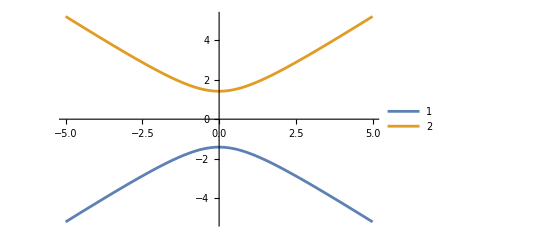

```mathematica
ClearAll;
sigma={PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};

dot[{a1_,a2_,a3_},{b1_,b2_,b3_}]:=a1*b1+ a2*b2+ a3*b3 

(*Note the m here is not  the same mass m we use, here it is a band paramter. b may not be the magnectif field either, but also just a band parameter *)
EF[kx_,ky_,m]:=  dot[sigma,{kx,ky,m}] ;


diham=EF [kx,ky,m];
diham//TraditionalForm
Length[ Eigenvectors[diham] ] 
band1=Eigenvalues[diham][[1]] ;
band2=Eigenvalues[diham][[2]] ;
band[n_]:=Eigenvalues[diham][[n]] ;
Plot[ {Eigenvalues[diham][[1]] /.m->2/.kz->0/.kx->1/.b->1,Eigenvalues[diham][[2]] /.m->2/.kz->0/.kx->1/.b->1},{ky,-5,5},PlotLegends->{"1","2","3","4"}]
```

#### Band functions

```mathematica
(*Bloch function un(k): un-normalised eigenvectors*)
u={{m-Sqrt[kx^2+ky^2+m^2],kx+I ky},{m+Sqrt[kx^2+ky^2+m^2],kx+I ky}};
 (*Bloch function un(k): normalised eigenvectors*)
nu={Normalize[{m-Sqrt[kx^2+ky^2+m^2],kx+I ky}]//FullSimplify[#,{m>0,kx∈Reals,ky∈Reals }]& ,Normalize[{m+Sqrt[kx^2+ky^2+m^2],kx+I ky}]//FullSimplify[#,{m>0,kx∈Reals,ky∈Reals }]& };
  (*Conjugate normalised eigenvectors*)cnu={Conjugate[nu[[1]]]//FullSimplify[#,{m>0,kx∈Reals,ky∈Reals }]& ,Conjugate[nu[[2]]]//FullSimplify[#,{m>0,kx∈Reals,ky∈Reals }]& };
```

```mathematica
cnu[[2]].nu[[1]]//FullSimplify[#,{m>0,kx∈Reals,ky∈Reals }]&
cnu[[1]].nu[[1]]//FullSimplify[#,{m>0,kx∈Reals,ky∈Reals }]&
```

(kx^2+ky^2+√(2+kx^2+ky^2+2 √(1+kx^2+ky^2))-√((1+kx^2+ky^2) (2+kx^2+ky^2+2 √(1+kx^2+ky^2))))/(2 √((kx^2+ky^2) (1+kx^2+ky^2)))

1

```mathematica
(*We define the non-abelian Berry connections and curvature*)
```

```mathematica
beconx=Table[I*(cnu[[n]].D[nu[[l]],kx] ),{n,1,2},{l,1,2}];
becony=Table[I*(cnu[[n]].D[nu[[l]],ky]) ,{n,1,2},{l,1,2}];
becurz=Table[D[ becony[[n,l]],kx] -D[ beconx[[n,l]],ky],{n,1,2},{l,1,2}];


becurz[[1,1]]//FullSimplify
becurz[[2,2]]//FullSimplify
```

1/(2 (1+kx^2+ky^2)^(3/2))

-1/(2 (1+kx^2+ky^2)^(3/2))

```mathematica
beconx[[1,1]]//FullSimplify
```

ky/(2 (1+kx^2+ky^2-√(1+kx^2+ky^2)))

```mathematica
(*matrix elements for canonical momentum/velocity*)
```

```mathematica
px=Table[KroneckerDelta[n,l]*D[band[n],{kx}]+I*beconx[[n,l]]*(band[n]-band[l]),{n,1,2},{l,1,2}];
py=Table[KroneckerDelta[n,l]*D[band[n],{ky}]+I*becony[[n,l]]*(band[n]-band[l]),{n,1,2},{l,1,2}];
```

## Schrodinger equation

```mathematica
(*Set up the initial value problem for the coeefcients*)
```

```mathematica
(*Initial coefceients of a1(kx,ky)*)
```

1

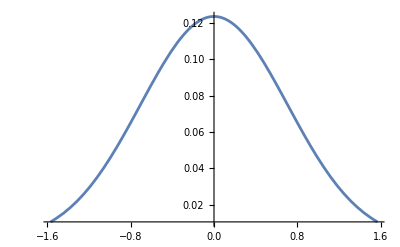

```mathematica
a10=E^(-(kx^2+ky^2))/(√π Erf[π/2])^2;
(*Check it is normalized*)
Integrate[a10,{kx,-Pi/2,Pi/2},{ky,-Pi/2,Pi/2}]
Plot[a10/.ky->1,{kx,-Pi/2,Pi/2},PlotRange->All]
```

### Exact result

```mathematica
Clear[a1,a2,m];
m=1;
sol=DSolve[{D[a1[t],t]==-I*a1[t]*(band1+beconx[[1,1]])-I*a2[t]*beconx[[1,2]],a1[0]==a10,D[a2[t],t]==-I*a2[t]*(band2+beconx[[2,2]])-I*a1[t]*beconx[[2,1]],a2[0]==0},{a1[t],a2[t]},{t,0,1}];
```

```mathematica
a1mod=Table[NIntegrate[Abs[a1[t]/.sol[[1]]],{kx,-Pi/2,Pi/2},{ky,-Pi/2,Pi/2},WorkingPrecision->20,Method->"GlobalAdaptive"],{t,0,10}];
a2mod=Table[NIntegrate[Abs[a2[t]/.sol[[1]]],{kx,-Pi/2,Pi/2},{ky,-Pi/2,Pi/2},WorkingPrecision->20,Method->"GlobalAdaptive"],{t,0,10}];
totmod=Table[a1mod[[i]]+a2mod[[i]],{i,1,Length[a1mod]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ky near {kx,ky} = {0.00109070774050207336599639960275357451694357969366492918619470528140542,0.00001011616707997664847304236900023756637436179218962205424415135371839412}. NIntegrate obtained 0.9669072324538450871045594580390385025255444515323973720711175247653009 and 8.243181190153132416552601607039291376118034426512594085594033389680672×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in ky near {kx,ky} = {0.002828850174122652234267510821522353299831072337558193226906016020517277,0.0000170423084453448963436937437930246018109189638375984502296700668177475}. NIntegrate obtained 0.9515435570012657422839247189903960202763198287462972448096469724118139 and 2.685864761706892616954334157932627058489354944504232226235059687452839×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ky near {kx,ky} = {0.004362830962008293464,0.000034084616890689792687}. NIntegrate obtained 0.9448374931177858373 and 4.5628229709023374383×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

$Aborted

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

$Aborted

NIntegrate::inumr: The integrand (ⅇ^Re[-kx^2-ky^2] Abs[-(ⅇ^((«1»)/(8 «4» √(«1»))) (-2 «3» (Times[«3»]+Times[«4»]+«8»+«9»)+«1»))/(√(-4 Plus[«746»]+Plus[«97»]^2))+(ⅇ^((«1»)/(«1»)) («1»+«1»))/(√(-4 Plus[«746»]+«1»))])/(π Erf[π/2]^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1.5707963267948966192,1.5707963267948966192},{-1.5707963267948966192,1.5707963267948966192}}.

$Aborted

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

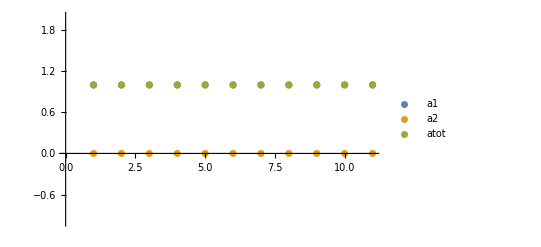

```mathematica
ListPlot[{a1mod,a2mod,totmod},PlotRange->{-1,2},PlotLegends->{a1,a2,atot}]
```

#### Example of Euler method

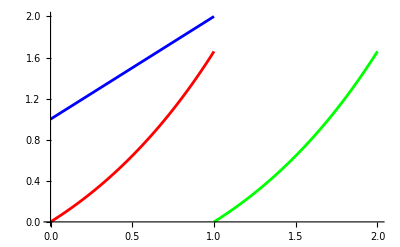

```mathematica
f[x_,y_]=1+y/x+(y/x)^2;
t[0]=0.;
x[0]=1.;
y[0]=0.;
t0=t[0];
tf=1.;
h=10^-3;
n=(tf-t0)/h;
Y1={{t[0],x[0]}};Y2={{t[0],y[0]}};Y3={{x[0],y[0]}};

For[i=0,i⩽n-1,i++,{t[i+1]=t[i]+h,x[i+1]=x[i]+h,y[i+1]=y[i]+h*f[x[i],y[i]],AppendTo[Y1,{t[i+1],x[i+1]}],AppendTo[Y2,{t[i+1],y[i+1]}],AppendTo[Y3,{x[i+1],y[i+1]}]}]

Show[ListLinePlot[Y1,PlotStyle->Blue,PlotRange->{{0,2},{0,2}}],ListLinePlot[Y2,PlotStyle->Red,PlotRange->{{0,2},{0,2}}],ListLinePlot[Y3,PlotStyle->Green,PlotRange->{{0,2},{0,2}}]]
```

#### Euler method

```mathematica
(* I*da1[t_]:=band1*a1[t,kx,ky]+Integrate[(*-I*D[a1[t,kx,ky],kx]*)+beconx[[1,1]]*a1[t,kx,ky]+beconx[[1,2]]*a2[t,kx,ky],{kx,-Pi/2,Pi/2},{ky,-Pi/2,Pi/2}];
  I*da2[t_]:=band2*a2[t,kx,ky]+Integrate[(*-I*D[a2[t,kx,ky],kx]*)+beconx[[2,1]]*a1[t,kx,ky]+beconx[[2,2]]*a2[t,kx,ky],{kx,-Pi/2,Pi/2},{ky,-Pi/2,Pi/2}];*)
```

#### Free case

```mathematica
Clear[a1,a2,da1,da2,A1,A2,h,m];
m=2;
t[0]=0.;
 t0=t[0];
tf=1.;
h=5^(-1);
n=(tf-t0)/h;
 a1[0,kx,ky]=a10;
 a2[0,kx,ky]=0.;
A1={{t[0], a1[0,kx,ky]}};
A2={{t[0], a2[0,kx,ky]}} ;
```

```mathematica
For[i=0,i⩽n-1,i++,{t[i+1]=t[i]+h, da1[i]=-I*a1[i,kx,ky]*band1,da2[i]=-I*a2[i,kx,ky]*band2,a1[i+1,kx,ky]= a1[i,kx,ky]+h*da1[i],a2[i+1,kx,ky]= a2[i,kx,ky]+h*da2[i],AppendTo[A1,{t[i+1],a1[i+1,kx,ky]}],AppendTo[A2,{t[i+1],a2[i+1,kx,ky]}] }]

a1mod=Table[{A1[[i,1]],NIntegrate[Abs[A1[[i,2]]],{kx,-Pi/2,Pi/2},{ky,-Pi/2,Pi/2} ]},{i,1,n+1}];
a2mod=Table[{A2[[i,1]],NIntegrate[Abs[A2[[i,2]]],{kx,-Pi/2,Pi/2},{ky,-Pi/2,Pi/2} ]},{i,1,n+1}];
```

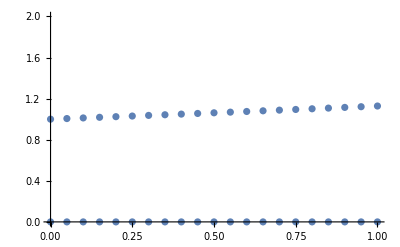

{{a1→Function[{t},(ⅇ^(-kx^2-ky^2+ⅈ √(4+kx^2+ky^2) t))/(π Erf[π/2]^2)],a2→Function[{t},0]}}

```mathematica
Show[ListPlot[a1mod,PlotRange->{0,2}],ListPlot[a2mod,PlotRange->{0,2}]]
```

#### In a field

```mathematica
Clear[m];
m=2;
Clear[A1,A2,da1,da2,a1,a2];
A1={{t[0], a1[0,kx,ky]}};
A2={{t[0], a2[0,kx,ky]}} ;
a1[0,kx,ky]=a10;
a2[0,kx,ky]=0.;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ky near {kx,ky} = {1.0811,0.0000101162}. NIntegrate obtained 2.62576-2.86589×10^-17 ⅈ and 5.67828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ky near {kx,ky} = {0.0000101162,-1.86806×10^-6}. NIntegrate obtained -6.72205×10^-18+1.38236×10^-18 ⅈ and 5.83922×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ky near {kx,ky} = {1.0811,0.0000101162}. NIntegrate obtained 2.62576-0.152871 ⅈ and 5.68803 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

$Aborted

$Aborted

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

$Aborted

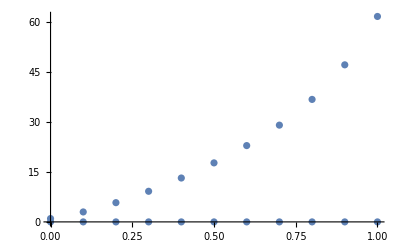

```mathematica
For[i=0,i⩽n-1,i++,{t[i+1]=t[i]+h,a1[i+1,kx,ky]= a1[i,kx,ky] - h*I*(band1*a1[i,kx,ky]+NIntegrate[(*-I*D[a1[t,kx,ky],kx]*)+beconx[[1,1]]*a1[i,kx,ky]+beconx[[1,2]]*a2[i,kx,ky],{kx,-Pi/2,Pi/2},{ky,-Pi/2,Pi/2}]),a2[i+1,kx,ky]= a2[i,kx,ky]-h* I*(band2*a2[i,kx,ky]+NIntegrate[(*-I*D[a2[t,kx,ky],kx]*)+beconx[[2,1]]*a1[i,kx,ky]+beconx[[2,2]]*a2[i,kx,ky],{kx,-Pi/2,Pi/2},{ky,-Pi/2,Pi/2}]),AppendTo[A1,{t[i+1],a1[i+1,kx,ky]}],AppendTo[A2,{t[i+1],a2[i+1,kx,ky]}] }]
A1[[All,2]]
A2[[All,2]]
a1mod=Table[{A1[[i,1]],NIntegrate[Abs[A1[[i,2]]],{kx,-Pi/2,Pi/2},{ky,-Pi/2,Pi/2}]},{i,1,n+1}];
a2mod=Table[{A2[[i,1]],NIntegrate[Abs[A2[[i,2]]],{kx,-Pi/2,Pi/2},{ky,-Pi/2,Pi/2}]},{i,1,n+1}];
Show[ListPlot[a1mod],ListPlot[a2mod]]
```

```mathematica
a1mod=Table[{A1[[i,1]],NIntegrate[Abs[A1[[i,2]]],{kx,-Pi/2,Pi/2},{ky,-Pi/2,Pi/2}]},{i,1,n+1}];
a2mod=Table[{A2[[i,1]],NIntegrate[Abs[A2[[i,2]]],{kx,-Pi/2,Pi/2},{ky,-Pi/2,Pi/2}]},{i,1,n+1}];
Show[ListPlot[a1mod],ListPlot[a2mod]]
```

Part::partw: Part 25 of {<<24092066256 bytes>>} does not exist.

$Aborted

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

$Aborted